## Előkészületek

szükséges adatok az adatok.nb fájlból:

```mathematica
normKoordExp={{0.,1.},{1.00003588865269,1.8647673389533383},{2.0128927502368232,3.5846809725240534},{3.012928638889512,7.491687863842094},{4.0129645275422,9.268044127917825},{5.013000416194889,7.322826972331486},{6.013036304847579,23.422042962641296},{7.0130721935002684,47.125116172869426},{8.013108082152955,44.00983374205759},{9.000322997874202,69.43329371467483}};
```

függvény létrehozása a hibaszámoláshoz:
 - hibafgv[f] inputja az az f függvény, mely eltérését akarjuk számolni az adatpontoktól
 - négyzetes hiba az adatpontok és a függvényértékek között (a legkisebb négyzetek elve alapján keres a FindFit algoritmus, amit az optimalizáláshoz használunk)

```mathematica
normKoordX=normKoordExp[[All,1]];
```

```mathematica
hibafgv[f_]=Total[((
Table[
{normKoordX[[i]],f[normKoordX[[i]]]},
{i,1,Length[normKoordExp]}
]
-normKoordExp)^2)
[[All,2]]
];
```

## Interaktív ábra

A csúszkákat mozgatva változtathatjuk a paramétereket az egyenletrendszerben

```mathematica
Manipulate[
sol=NDSolve[
{T'[t]==r*T[t](1-T[t]/kT)-δ*T[t]*c[t],
c'[t]==-λ*c[t]*b[t],
b'[t]==0,
T[0]==T0,c[0]==0,b[0]==B0,
WhenEvent[{t==4,t==7},c[t]->c[t]+Cplusz]},
{T,c,b},
{t,9.1}
];
fgvPontok=Table[{normKoordX[[i]],(T[normKoordX[[i]]]/T0)/.sol[[1]]},{i,1,Length[normKoordExp]}];
hiba=Total[((fgvPontok-normKoordExp)^2)[[All,2]]];
Column[{
Show[
LogPlot[
Evaluate[(T[t]/T0)/.sol[[1]]],
{t,0,9.1},
PlotRange->{{0,10},{1,100}},
PlotLegends->{"T(t)"},
AxesLabel->{"t",None},
AxesOrigin->{0,1},
ImageSize->400
],
ListLogPlot[
normKoordExp,
PlotRange->{{0,10},{1,100}},
PlotLegends->{"adatsor"},
Joined->True,
AxesOrigin->{0,1},
PlotMarkers->Automatic,
PlotStyle->Red
]
],
Text[StringJoin["négyzetes hiba: ",ToString[NumberForm[hiba]]]],
Text["függvénypontok:"],
fgvPontok,
Text["eltérés:"],
fgvPontok-normKoordExp
}],
Style["Konstans baktériumpopuláció, kemoterápia 4+7. nap", 12],
Delimiter,
{{r,0.6,"r"},0,4,Appearance->"Labeled"},
{{kT,400,"K_T"},0,1000,Appearance->"Labeled"},
{{δ,0.82,"δ"},0,5,Appearance->"Labeled"},
{{λ,3.9,"λ"},0,4,Appearance->"Labeled"},
Delimiter,
{{T0,1,"T_0"},0,10,Appearance->"Labeled"},
{{B0,22,"B_0"},0,100,Appearance->"Labeled"},
{{Cplusz,45,"p"},0,100,Appearance->"Labeled"},
ControlPlacement->{Left,Left,Left,Left,Left,Left,Left}
]
```

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

Part::partd: Part specification normKoordX⟦1⟧ is longer than depth of object.

Part::partd: Part specification normKoordX⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification normKoordX⟦1⟧ is longer than depth of object.

Part::partd: Part specification normKoordX⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification normKoordX⟦1⟧ is longer than depth of object.

Part::partd: Part specification normKoordX⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

ListLogPlot::lpn: normKoordExp is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListLogPlot[normKoordExp,PlotRange→{{0,10},{1,100}},PlotLegends→{adatsor},Joined→True,AxesOrigin→{0,1},PlotMarkers→Automatic,PlotStyle→RGBColor[1, 0, 0]]].

## Illesztés

A fenti interaktív ábra csúszkáit kézzel állítgatva a következő paramétereknél találtunk minimumot:  r = 0.6, K_T = 400, δ = 0.82, λ = 3.9, T_0 = 1, B_0 = 22, p = 45. Így kiinduláshoz ezeket a B_0 és p értékeket fogjuk használni.
A dolgozatban kifejtett okok miatt a második adag gyógyszert nem a 9. napon, hanem hamarabb, a 7. nap környékén adjuk be. Azért ezt a napot választottuk, mert a grafikonon a 7. nap után tapasztaltunk olyan visszaesést a tumorméretben, mint a 4. nap után, ahol az első adag gyógyszer lett beadva.

### Illesztés fix p paraméter és fix napok esetén

A gyógyszer beadandó p mennyiségét fixáljuk, és úgy optimalizáljuk a maradék paramétert.

```mathematica
Clear[model,fit]
```

```mathematica
B0=22;p=45;
```

```mathematica
model[r_?NumberQ,kT_?NumberQ,δ_?NumberQ,λ_?NumberQ]:=
(model[r,kT,δ,λ]=First[T/.NDSolve[
{T'[t]==r*T[t](1-T[t]/kT)-δ*T[t]*c[t],
c'[t]==-λ*c[t]*b[t],
b'[t]==0,
T[0]==1,c[0]==0,b[0]==B0,
WhenEvent[{t==4,t==7},c[t]->c[t]+p]},
T,
{t,0,9.1}
]])
```

Először a paraméterek pozitivitását leszámítva nem teszünk semmilyen feltételezést:

```mathematica
fit=FindFit[normKoordExp,{model[r,kT,δ,λ][t],{r>0,kT>0,δ>0,λ>0}},{r,kT,δ,λ},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.661103,kT→1476.05,δ→0.0365893,λ→0.0925482}

```mathematica
tfgv=model[r,kT,δ,λ]/.fit
```

InterpolatingFunction[…]

#### Próbák: különböző megkötések a paraméterekre

Számos egyéb megkötést, illetve azok különböző kombinációit is megpróbáltunk.  Ezek közül a legjobbak:

```mathematica
fit2=FindFit[normKoordExp,{model[r,kT,δ,λ][t],{r>0,kT>1000,δ>0,λ>0}},{r,kT,δ,λ},t,Method->"NMinimize",AccuracyGoal->4,PrecisionGoal->4]
```

{r→0.660755,kT→1001.8,δ→0.037231,λ→0.0966802}

```mathematica
tfgv2=model[r,kT,δ,λ]/.fit2
```

InterpolatingFunction[…]

```mathematica
fit3=FindFit[normKoordExp,{model[r,kT,δ,λ][t],{r>0,kT>400,0<δ<1,0<λ<1}},{r,kT,δ,λ},t,Method->"NMinimize",AccuracyGoal->4,PrecisionGoal->4]
```

{r→0.659587,kT→400.538,δ→0.0416369,λ→0.122699}

```mathematica
tfgv3=model[r,kT,δ,λ]/.fit3
```

InterpolatingFunction[…]

```mathematica
fit4=FindFit[normKoordExp,{model[r,kT,δ,λ][t],{r>0,kT>400,δ>0,λ>0}},{r,kT,δ,λ},t,Method->"NMinimize",AccuracyGoal->4,PrecisionGoal->4]
```

{r→0.662961,kT→400.,δ→0.0784022,λ→0.231704}

```mathematica
tfgv4=model[r,kT,δ,λ]/.fit4
```

InterpolatingFunction[…]

A kapott függvények ábrázolása és a hozzájuk tartozó hibák kiszámítása:

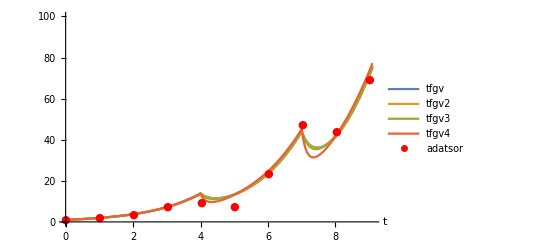
-Graphics-1. hiba: 80.2798
2. hiba: 79.0944
3. hiba: 75.673
4. hiba: 84.7929

```mathematica
Row[{
Show[
Plot[
{tfgv[t],tfgv2[t],tfgv3[t],tfgv4[t]},
{t,0,9.1},
PlotRange->{{0,9.1},{0,100}},
PlotLegends->{"tfgv","tfgv2","tfgv3","tfgv4"},
AxesLabel->{"t",None},
ImageSize->400
],
ListPlot[
{normKoordExp},
PlotRange->{{0,9.1},{0,100}},
PlotStyle->{Red},
PlotMarkers->{"●"},
PlotLegends->{"adatsor"}
]
],
Column[{
Text[StringJoin["1. hiba: ",ToString[NumberForm[hibafgv[tfgv]]]]],
Text[StringJoin["2. hiba: ",ToString[NumberForm[hibafgv[tfgv2]]]]],
Text[StringJoin["3. hiba: ",ToString[NumberForm[hibafgv[tfgv3]]]]],
Text[StringJoin["4. hiba: ",ToString[NumberForm[hibafgv[tfgv4]]]]]
}]
},"              "]
```

### Illesztés fix p paraméter és optimalizálandó napok esetén

A gyógyszer beadandó p mennyiségét fixáljuk, és úgy optimalizáljuk a maradék paramétert, amik közé a kezelések időpontját is felvesszük.

```mathematica
Clear[modeln,fitn]
```

```mathematica
B0n=22;pn=45;
```

```mathematica
modeln[r_?NumberQ,kT_?NumberQ,δ_?NumberQ,λ_?NumberQ,elso_?NumberQ,mas_?NumberQ]:=
(modeln[r,kT,δ,λ,elso,mas]=First[T/.NDSolve[
{T'[t]==r*T[t](1-T[t]/kT)-δ*T[t]*c[t],
c'[t]==-λ*c[t]*b[t],
b'[t]==0,
T[0]==1,c[0]==0,b[0]==B0n,
WhenEvent[{t==elso,t==mas},c[t]->c[t]+pn]},
T,
{t,0,9.1}
]])
```

Először a paraméterek pozitivitását leszámítva nem teszünk semmilyen feltételezést, leszámítva a kezelések időpontját. A grafikont tanulmányozva az első adag időpontját 3.8 és 4.5 nap, míg a második adag időpontját 6.8 és 7.5 nap közé szorítjuk. Ezzel minden optimalizálásnál élünk.

```mathematica
fitn=FindFit[normKoordExp,{modeln[r,kT,δ,λ,elso,mas][t],{r>0,kT>0,δ>0,λ>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.649757,kT→73.856,δ→1.21761,λ→36.6728,elso→4.00677,mas→7.01307}

```mathematica
tfgvn=modeln[r,kT,δ,λ,elso,mas]/.fitn
```

InterpolatingFunction[…]

#### Próbák: különböző megkötések a paraméterekre

Számos egyéb megkötést, illetve azok különböző kombinációit is megpróbáltunk.  Ezek közül a legjobbak:

```mathematica
fitn2=FindFit[normKoordExp,{modeln[r,kT,δ,λ,elso,mas][t],{r>0,kT>400,δ>0,λ>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.686689,kT→51831.9,δ→0.0631198,λ→0.132516,elso→3.8,mas→7.5}

```mathematica
tfgvn2=modeln[r,kT,δ,λ,elso,mas]/.fitn2
```

InterpolatingFunction[…]

```mathematica
fitn3=FindFit[normKoordExp,{modeln[r,kT,δ,λ,elso,mas][t],{r>0,kT>1000,δ>0,λ>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.669912,kT→1000.82,δ→0.557101,λ→1.40693,elso→3.98725,mas→7.5}

```mathematica
tfgvn3=modeln[r,kT,δ,λ,elso,mas]/.fitn3
```

InterpolatingFunction[…]

```mathematica
fitn4=FindFit[normKoordExp,{modeln[r,kT,δ,λ,elso,mas][t],{r>0.6,kT>400,δ>1,λ>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.662481,kT→400.,δ→1.06733,λ→3.11061,elso→4.00067,mas→7.37043}

```mathematica
tfgvn4=modeln[r,kT,δ,λ,elso,mas]/.fitn4
```

InterpolatingFunction[…]

```mathematica
fitn5=FindFit[normKoordExp,{modeln[r,kT,δ,λ,elso,mas][t],{r>0.6,kT>400,δ>0,λ>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{r→0.663158,kT→400.166,δ→0.602677,λ→1.73009,elso→3.99249,mas→7.01307}

```mathematica
tfgvn5=modeln[r,kT,δ,λ,elso,mas]/.fitn5
```

InterpolatingFunction[…]

A kapott függvények ábrázolása és a hozzájuk tartozó hibák kiszámítása:

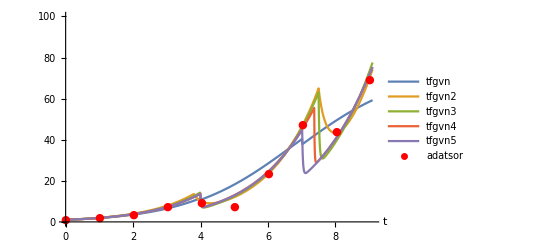
-Graphics-1. hiba: 342.852
2. hiba: 24.7869
3. hiba: 65.7942
4. hiba: 54.0819
5. hiba: 53.8957

```mathematica
Row[{
Show[
Plot[
{tfgvn[t],tfgvn2[t],tfgvn3[t],tfgvn4[t],tfgvn5[t]},
{t,0,9.1},
PlotRange->{{0,9.1},{0,100}},
PlotLegends->{"tfgvn","tfgvn2","tfgvn3","tfgvn4","tfgvn5"},
AxesLabel->{"t",None},
ImageSize->400
],
ListPlot[
{normKoordExp},
PlotRange->{{0,9.1},{0,100}},
PlotStyle->{Red},
PlotMarkers->{"●"},
PlotLegends->{"adatsor"}
]
],
Column[{
Text[StringJoin["1. hiba: ",ToString[NumberForm[hibafgv[tfgvn]]]]],
Text[StringJoin["2. hiba: ",ToString[NumberForm[hibafgv[tfgvn2]]]]],
Text[StringJoin["3. hiba: ",ToString[NumberForm[hibafgv[tfgvn3]]]]],
Text[StringJoin["4. hiba: ",ToString[NumberForm[hibafgv[tfgvn4]]]]],
Text[StringJoin["5. hiba: ",ToString[NumberForm[hibafgv[tfgvn5]]]]]
}]
},"              "]
```

### Illesztés optimalizálandó p paraméter és napok esetén

Már a gyógyszer beadandó mennyiségét sem fixáljuk, és úgy optimalizáljuk a maradék paramétert, amik közé a kezelések időpontját is felvesszük.

```mathematica
Clear[modelpn,fitpn]
```

```mathematica
baktpn=22;
```

```mathematica
modelpn[r_?NumberQ,kT_?NumberQ,δ_?NumberQ,λ_?NumberQ,ppn_?NumberQ,elso_?NumberQ,mas_?NumberQ]:=
(modelpn[r,kT,δ,λ,ppn,elso,mas]=First[T/.NDSolve[
{T'[t]==r*T[t](1-T[t]/kT)-δ*T[t]*c[t],
c'[t]==-λ*c[t]*b[t],
b'[t]==0,
T[0]==1,c[0]==0,b[0]==baktpn,
WhenEvent[{t==elso,t==mas},c[t]->c[t]+ppn]},
T,
{t,0,9.1}
]])
```

Először a paraméterek pozitivitását leszámítva nem teszünk semmilyen feltételezést, leszámítva a kezelések időpontját. A grafikont tanulmányozva az első adag időpontját 3.8 és 4.5 nap, míg a második adag időpontját 6.8 és 7.5 nap közé szorítjuk. Ezzel minden optimalizálásnál élünk.

```mathematica
fitpn=FindFit[normKoordExp,{modelpn[r,kT,δ,λ,ppn,elso,mas][t],{r>0,kT>0,δ>0,λ>0,ppn>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,ppn,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.646022,kT→2746.46,δ→9.92827,λ→19.3847,ppn→31.8579,elso→4.46719,mas→7.5}

```mathematica
{rt->0.6656129391208399,k->264.1176577029142,δ->15.177050157647326,λ->20.567162617436658,Cplusz->19.48975956692788,elso->3.9630831380710996,mas->7.013072193621111}
```

```mathematica
tfgvpn=modelpn[r,kT,δ,λ,ppn,elso,mas]/.fitpn
```

InterpolatingFunction[…]

#### Próbák: különböző megkötések a paraméterekre

Számos egyéb megkötést, illetve azok különböző kombinációit is megpróbáltunk.  Ezek közül a legjobbak:

```mathematica
fitpn2=FindFit[normKoordExp,{modelpn[r,kT,δ,λ,ppn,elso,mas][t],{r>0,kT>0,0<δ<1,0<λ<1,ppn>40,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,ppn,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.664543,kT→102.913,δ→0.095226,λ→0.707253,ppn→52.93,elso→3.8,mas→7.01307}

```mathematica
tfgvpn2=modelpn[r,kT,δ,λ,ppn,elso,mas]/.fitpn2
```

InterpolatingFunction[…]

```mathematica
fitpn3=FindFit[normKoordExp,{modelpn[r,kT,δ,λ,ppn,elso,mas][t],{r>0.65,0<kT<1000,δ>10,λ>10,ppn>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,ppn,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.664639,kT→258.541,δ→10.0269,λ→10.,ppn→14.1772,elso→3.82473,mas→7.01307}

```mathematica
tfgvpn3=modelpn[r,kT,δ,λ,ppn,elso,mas]/.fitpn3
```

InterpolatingFunction[…]

```mathematica
fitpn4=FindFit[normKoordExp,{modelpn[r,kT,δ,λ,ppn,elso,mas][t],{r>0.65,0<kT<1000,δ>0,λ>0,ppn>0,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,ppn,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

NMinimize::nnum: The function value «1»[{0.655571,0,6.10895,4.08241,5.31686,3.8,7.5}] is not a number at {elso,kT,mas,ppn,r,δ,λ} = {3.8,0.,7.5,5.31686,0.655571,6.10895,4.08241}.

{r→0.650119,kT→283.228,δ→7.15677,λ→2.29532,ppn→4.23011,elso→3.81725,mas→7.13003}

```mathematica
tfgvpn4=modelpn[r,kT,δ,λ,ppn,elso,mas]/.fitpn4
```

InterpolatingFunction[…]

```mathematica
fitpn5=FindFit[normKoordExp,{modelpn[r,kT,δ,λ,ppn,elso,mas][t],{r>0,kT>400,δ>0,λ>0,ppn>20,3.8<elso<4.5,6.8<mas<7.5}},{r,kT,δ,λ,ppn,elso,mas},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{r→0.665339,kT→400.076,δ→0.934565,λ→1.19843,ppn→20.3417,elso→3.98103,mas→7.01307}

```mathematica
tfgvpn5=modelpn[r,kT,δ,λ,ppn,elso,mas]/.fitpn5
```

InterpolatingFunction[…]

A kapott függvények ábrázolása és a hozzájuk tartozó hibák kiszámítása:

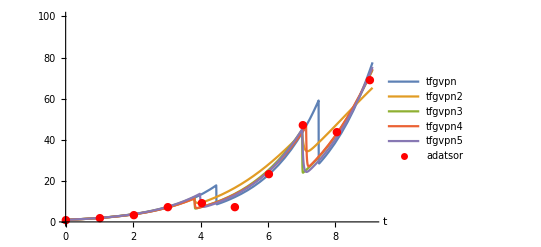
-Graphics-1. hiba: 90.2677
2. hiba: 163.492
3. hiba: 57.0929
4. hiba: 60.0577
5. hiba: 53.7936

```mathematica
Row[{
Show[
Plot[
{tfgvpn[t],tfgvpn2[t],tfgvpn3[t],tfgvpn4[t],tfgvpn5[t]},
{t,0,9.1},
PlotRange->{{0,9.1},{0,100}},
PlotLegends->{"tfgvpn","tfgvpn2","tfgvpn3","tfgvpn4","tfgvpn5"},
AxesLabel->{"t",None},
ImageSize->400
],
ListPlot[
{normKoordExp},
PlotRange->{{0,9.1},{0,100}},
PlotStyle->{Red},
PlotMarkers->{"●"},
PlotLegends->{"adatsor"}
]
],
Column[{
Text[StringJoin["1. hiba: ",ToString[NumberForm[hibafgv[tfgvpn]]]]],
Text[StringJoin["2. hiba: ",ToString[NumberForm[hibafgv[tfgvpn2]]]]],
Text[StringJoin["3. hiba: ",ToString[NumberForm[hibafgv[tfgvpn3]]]]],
Text[StringJoin["4. hiba: ",ToString[NumberForm[hibafgv[tfgvpn4]]]]],
Text[StringJoin["5. hiba: ",ToString[NumberForm[hibafgv[tfgvpn5]]]]]
}]
},"              "]
```

## Konklúzió és további optimalizálások

Megállapíthatjuk, hogy akkor kaptuk a legkisebb hibát, mikor lefixáltuk a gyógyszer p mennyiségét, de a kezelések időpontját is optimalizálandó paraméternek tekintettük. Ekkor a legjobban illeszkedő függvényünk a tfgvn2 volt, ahol
 - a megkötések: r>0, K_T>400, δ>0, λ>0, 3.8<elso<4.5, 6.8<mas<7.5
 - a kapott paraméterek: r→0.686689,K_T→51831.9,δ→0.0631198,λ→0.132516,elso→3.8,mas→7.5
 - a négyzetes hiba: 24.7869.

Külön a legjobb illesztés és az adatsor ábrázolása:

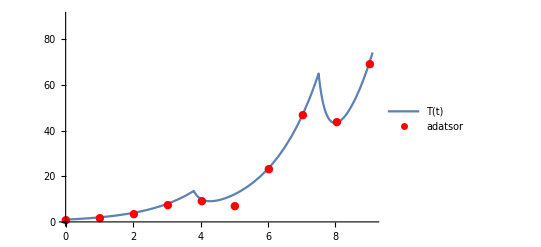

```mathematica
Show[
Plot[
{tfgvn2[t]},
{t,0,9.1},
PlotRange->{{0,9.1},{0,90}},
PlotLegends->{"T(t)"}
],
ListPlot[
{normKoordExp},
PlotRange->{{0,9.1},{0,90}},
PlotMarkers->{"●"},
PlotStyle->{Red},
PlotLegends->{"adatsor"},
AxesLabel->{"t",None}
]
]
```

### Külön a p paraméter optimalizálása

Az így kapott paramétereket lefixálva optimalizálhatjuk csak a p értéket, hátha tudunk javítani.

```mathematica
Clear[modelc,fitc]
```

```mathematica
baktc=22;
```

```mathematica
modelc[p_?NumberQ]:=
(modelc[p]=First[T/.NDSolve[
{T'[t]==0.686689411498072*T[t](1-T[t]/51831.90592461847)-0.06311980122430769*T[t]*c[t],
c'[t]==-0.13251568493859608*c[t]*b[t],
b'[t]==0,
T[0]==1,c[0]==0,b[0]==baktc,
WhenEvent[{t==3.8,t==7.5},c[t]->c[t]+p]},
T,
{t,0,9.1}
]])
```

```mathematica
fitc=FindFit[normKoordExp,{modelc[p][t],{0<p}},{p},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize"]
```

{p→44.9999}

Láthatjuk, hogy gyakorlatilag az eredeti p=45 értéket kapjuk vissza, azaz így nem tudunk javítani.

### Módosított Hill-függvény használata

Módosítjuk a modellt: a kemoterápiás gyógyszer nem a saját mennyiségével arányosan pusztítja a baktériumokat, hanem a Hill-függvény egy változatát írjuk bele az egyenletbe.
Fixáljuk a fentiekben optimalizált p gyógyszermennyiséget, valamint a kezelések időpontjának a 3.8. és 7.5. napot.

```mathematica
Clear[modelm,fitm]
```

```mathematica
baktm=22;pm=45;
```

```mathematica
modelm[r_?NumberQ,kT_?NumberQ,δ_?NumberQ,λ_?NumberQ,m_?NumberQ,n1_?NumberQ,n2_?NumberQ]:=
(modelm[r,kT,δ,λ,m,n1,n2]=First[T/.NDSolve[
{T'[t]==r*T[t](1-T[t]/kT)-δ*T[t]*((c[t])^n1/(m+(c[t])^n2)),
c'[t]==-λ*c[t]*b[t],
b'[t]==0,
T[0]==1,c[0]==0,b[0]==baktm,
WhenEvent[{t==3.8,t==7.5},c[t]->c[t]+pm]},
T,
{t,0,9.1}
]])
```

Először a paraméterek pozitivitását leszámítva nem teszünk semmilyen feltételezést.

```mathematica
fitm=FindFit[normKoordExp,{modelm[r,kT,δ,λ,m,n1,n2][t],{0<r,0<kT,0<δ,0<λ,0<m,0<n1,0<n2}},{r,kT,δ,λ,m,n1,n2},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize",NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)]
```

NMinimize::nnum: The function value «1»[{1.47998,13.5857,0.0308484,0,0,2.27977,21.9922}] is not a number at {kT,m,n1,n2,r,δ,λ} = {13.5857,0.,2.27977,21.9922,1.47998,0.0308484,0.}.

{r→1.29661,kT→16.8176,δ→9.91443×10^-8,λ→36.8854,m→8.85654,n1→3.14283,n2→25.8516}

```mathematica
tfgvm=modelm[r,kT,δ,λ,m,n1,n2]/.fitm
```

InterpolatingFunction[…]

#### Próbák: különböző megkötések a paraméterekre

Számos egyéb megkötést, illetve azok különböző kombinációit is megpróbáltunk.  Ezek közül a legjobbak:

```mathematica
fitm2=FindFit[normKoordExp,{modelm[r,kT,δ,λ,m,n1,n2][t],{0<r,400<kT,0<δ,0<λ,0<m,0<n1,0<n2}},{r,kT,δ,λ,m,n1,n2},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize",NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)]
```

{r→0.647823,kT→400.264,δ→3.51431,λ→1.28361,m→0.0618415,n1→1.19111,n2→1.57268}

```mathematica
tfgvm2=modelm[r,kT,δ,λ,m,n1,n2]/.fitm2
```

InterpolatingFunction[…]

```mathematica
fitm3=FindFit[normKoordExp,{modelm[r,kT,δ,λ,m,n1,n2][t],{0<r,400<kT,0<δ,0<λ,0.1<m,0<n1,0<n2}},{r,kT,δ,λ,m,n1,n2},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize",NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)]
```

{r→0.651459,kT→405.122,δ→5.05133,λ→1.17022,m→1.25404,n1→0.242062,n2→2.3195}

```mathematica
tfgvm3=modelm[r,kT,δ,λ,m,n1,n2]/.fitm3
```

InterpolatingFunction[…]

```mathematica
fitm4=FindFit[normKoordExp,{modelm[r,kT,δ,λ,m,n1,n2][t],{0<r,5000<kT,0<δ,0<λ,0<m,0<n1,0<n2}},{r,kT,δ,λ,m,n1,n2},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize",NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)]
```

{r→0.635188,kT→5000.72,δ→5.24266,λ→1.58303,m→1.11623,n1→0.195973,n2→2.25118}

```mathematica
tfgvm4=modelm[r,kT,δ,λ,m,n1,n2]/.fitm4
```

InterpolatingFunction[…]

```mathematica
fitm5=FindFit[normKoordExp,{modelm[r,kT,δ,λ,m,n1,n2][t],{0<r,5000<kT,0<δ,0<λ,0<m,1<n1,1<n2}},{r,kT,δ,λ,m,n1,n2},t,PrecisionGoal->4,AccuracyGoal->4,Method->"NMinimize",NormFunction->(Re[#].Re[#]+Im[#].Im[#]&)]
```

NMinimize::nnum: The function value Experimental`NumericalFunction[«1»][{0.518405,5000.,«3»,1.46038,1.55103}] is not a number at {kT,m,n1,n2,r,δ,λ} = {5000.,0.,1.46038,1.55103,0.518405,2.00266,0.25321}.

{r→0.669482,kT→5000.,δ→1.99702,λ→1.04967,m→9.88817×10^-8,n1→1.78195,n2→1.54451}

```mathematica
tfgvm5=modelm[r,kT,δ,λ,m,n1,n2]/.fitm5
```

InterpolatingFunction[…]

A kapott függvények ábrázolása és a hozzájuk tartozó hibák kiszámítása:

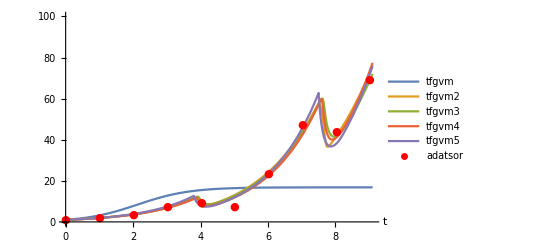
-Graphics-1. hiba: 4642.28
2. hiba: 59.2462
3. hiba: 52.4147
4. hiba: 68.2746
5. hiba: 67.2765

```mathematica
Row[{
Show[
Plot[
{Re[tfgvm[t]],Re[tfgvm2[t]],Re[tfgvm3[t]],Re[tfgvm4[t]],Re[tfgvm5[t]]},
{t,0,9.1},
PlotRange->{{0,9.1},{0,100}},
PlotLegends->{"tfgvm","tfgvm2","tfgvm3","tfgvm4","tfgvm5"},
AxesLabel->{"t",None},
ImageSize->400
],
ListPlot[
{normKoordExp},
PlotRange->{{0,9.1},{0,100}},
PlotStyle->{Red},
PlotMarkers->{"●"},
PlotLegends->{"adatsor"}
]
],
Column[{
Text[StringJoin["1. hiba: ",ToString[NumberForm[Abs[hibafgv[tfgvm]]]]]],
Text[StringJoin["2. hiba: ",ToString[NumberForm[Abs[hibafgv[tfgvm2]]]]]],
Text[StringJoin["3. hiba: ",ToString[NumberForm[Abs[hibafgv[tfgvm3]]]]]],
Text[StringJoin["4. hiba: ",ToString[NumberForm[Abs[hibafgv[tfgvm4]]]]]],
Text[StringJoin["5. hiba: ",ToString[NumberForm[Abs[hibafgv[tfgvm5]]]]]]
}]
},"              "]
```